# Generate and export a series of figures on RAP methodologies for Supplemental Material

## Harold Thimbleby, 2023

```mathematica
imageType="jpg";
```

```mathematica
runningAsNotebook=MatchQ[$FrontEnd,FrontEndObject[_]];
If[runningAsNotebook,SetDirectory[NotebookDirectory[]]]
```

/Users/harold/Organised/Active papers/Ignorance/Computational Science Computer Journal/programs

```mathematica
faceColor=Lighter[Gray,.9];
face=FaceForm[faceColor];
```

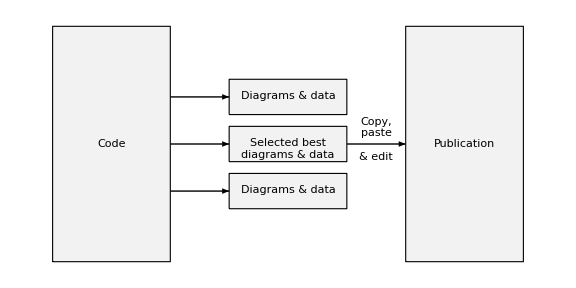

```mathematica
schematic=Graphics[{
Black,EdgeForm[Black],face,
Rectangle[{0,0},{1,2},RoundingRadius->.1],Text[Style["Code",Large],{.5,1}],
n=5;
height=2/n;
gap=.5/n;
Table[
{base=i*height+gap/2;
middle=base+(height-gap)/2;
Thick,Arrow[{{1,middle},{1.5,middle}}],
Rectangle[{1.5,base},{2.5,(i+1)*height-gap/2}],
Text[
If[i==2,"Selected best\ndiagrams & data","Diagrams & data"],{2,i*height+gap/2+height/2},{0,.5}],
If[i==2,{
Arrow[{{2.5,middle},{3,middle}}],
Text["Copy,\npaste\n\n& edit",{2.75,middle+.04}]
},{}]
},
{i,1,n-2}
],
Rectangle[{3,0},{4,2},RoundingRadius->.1],Text[Style["Publication",Large],{3.5,1}]
},ImageSize->Large
]
```

```mathematica
Export["../generated/basic."<>imageType,schematic]
```

../generated/basic.jpg

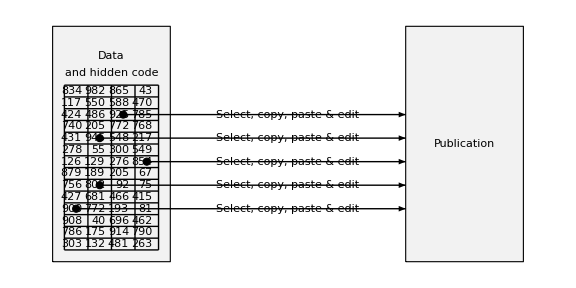

If you like the result, copy this data to the newPositions assignment, and set i to 1
{0.2,0.4,0.8,0.4,0.6}

```mathematica
data={};
newPositions={0.2,0.4,0.8,0.4,0.6}; (* nice results from a previous run *)
i=1; (* set to 1 to use values stored in newPositions; set to 0 to generate new positions *)
schematic=Graphics[{
Black,EdgeForm[Black],face,
Rectangle[{0,0},{1,2},RoundingRadius->.1],Text[Style["Data",Large],{.5,1.75}],
Text[Style["and hidden code",Medium],{.5,1.6}],
Table[Line[{{x,0.1},{x,1.5}}],{x,0.1,0.9,.2}],
Table[Line[{{0.1,y},{0.9,y}}],{y,0.1,1.5,.1}],
Table[Text[RandomInteger[{0,999}],{x+.15,y+.05},{1,0}],{x,0.1,0.8,.2},{y,0.1,1.4,.1}],
Table[{
If[i<1,
head=0.2*RandomInteger[{0,3}]+0.2,
head=newPositions[[i++]]
];
AppendTo[data,head];
FaceForm[Black],Disk[{head,y},.03],
Thick,
Arrow[{{head,y},{3,y}}],
Text[Style["  Select, copy, paste & edit  ",Medium,Background->White],{2,y}]},
{y,.45,1.3,.2}],
Rectangle[{3,0},{4,2},RoundingRadius->.1],Text[Style["Publication",Large],{3.5,1}]
},ImageSize->Large
];
If[runningAsNotebook,
Print[schematic];
Print["If you like this result, copy this data to the newPositions assignment, and set i to 1\n",data]
];
```

```mathematica
Export["../generated/excel."<>imageType,schematic]
```

../generated/excel.jpg

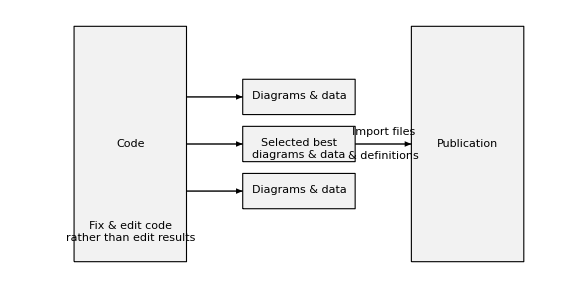

```mathematica
schematic=Graphics[{
Black,face,EdgeForm[Black],
Rectangle[{0,0},{1,2},RoundingRadius->.1],Text[Style["Code",Large],{.5,1}],
Text["Fix & edit code\nrather than edit results",{0.5,.25}],
n=5;
height=2/n;
gap=.5/n;
Table[
{base=i*height+gap/2;
middle=base+(height-gap)/2;
Thick,Arrow[{{1,middle},{1.5,middle}}],
Rectangle[{1.5,base},{2.5,(i+1)*height-gap/2}],
Text[
If[i==2,"Selected best\ndiagrams & data","Diagrams & data"],{2,i*height+gap/2+height/2},{0,.5}],
If[i==2,{
Arrow[{{2.5,middle},{3,middle}}],
Text["Import files\n\n& definitions",{2.75,middle}]
},{}]
},
{i,1,n-2}
],
Rectangle[{3,0},{4,2},RoundingRadius->.1],Text[Style["Publication",Large],{3.5,1}]
},ImageSize->Large
]
```

```mathematica
Export["../generated/import."<>imageType,schematic]
```

../generated/import.jpg

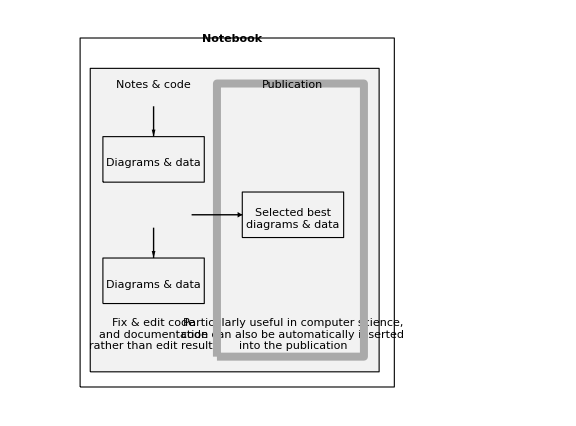

```mathematica
schematic=Graphics[{
Black,face,EdgeForm[Black],
Rectangle[{0,0},{2.85,2},RoundingRadius->.1],Text[Style["Notes & code",Large],{0.125+.5,1.9}],
Text["Fix & edit code\nand documentation\nrather than edit results",{0.625,.25}],
Text["Particularly useful in computer science,\ncode can also be automatically inserted\ninto the publication",{2,.25}],
n=5;
height=2/n;
gap=.5/n;
FaceForm[None],
{EdgeForm[Directive[Thickness[.01],Lighter@Gray,CapForm["Round"],Dashing[{.02,.03}]]],
Rectangle[{1.25,0+d},{2.7,2-d},RoundingRadius->.1]},
Table[
{base=i*height+gap/2;
middle=base+(height-gap)/2;
raiseArrow=.035;(* tinker to get the arrow to miss the rectangle border's dashes *)
top=(i+1)*height-gap/2;
xpos=If[i==2,1.5,0.125];
Thick,
If[i≠2,{Arrow[{{xpos+.5,top+2gap},{xpos+.5,top}}],Rectangle[{xpos,base},{xpos+1,top}]},{
Arrow[{{1,middle+raiseArrow},{1.5,middle+raiseArrow}}],Rectangle[{xpos,base+raiseArrow},{xpos+1,top+raiseArrow}]
}],
Text[
If[i==2,"Selected best\ndiagrams & data","Diagrams & data"],{xpos+.5,i*height+gap/2+height/2+If[i==2,raiseArrow,-raiseArrow]},{0,.5}],
If[False,{
Arrow[{{xpos+1,middle},{xpos+1.5,middle}}],
Text["Import files\n\n& definitions",{2.75,middle}]
},{}]
},
{i,1,n-2}
],
d=.1;
Text[Style["  Publication  ",Background->faceColor,Large],{2,1.9}],EdgeForm[Dashing[{1,0}]],
Rectangle[{-.1,-.1},{3,2.2},RoundingRadius->.2],
Text[Style["  Notebook  ",Bold,Large,Background->White],{1.4,2.2}]
},ImageSize->Large
]
```

```mathematica
Export["../generated/notebook."<>imageType,schematic]
```

../generated/notebook.jpg